```mathematica
reflect[d_,n_]:=d-2(d.n)n

shininess=.;
normal={0,0,1};
angleBetween[a_,b_]:=a.b
phongShade[lightdir_,viewdir_]:=kd*(lightdir.normal)+ks*(reflect[lightdir,normal].viewdir)^shininess
lightdir=FromSphericalCoordinates[{1,Subscript[θ, i],Subscript[ϕ, i]}];
viewdir=FromSphericalCoordinates[{1,Subscript[θ, v],Subscript[ϕ, v]}];
phongShadeAngular=phongShade[lightdir,viewdir]//FullSimplify;
```

```mathematica
lockTheta=phongShadeAngular/.{Subscript[θ, v]->Pi/4,Subscript[θ, i]->Pi/4}//FullSimplify
%/.Subscript[ϕ, i]->0;
Integrate[%,{Subscript[ϕ, v],-Pi,Pi}]
totalEnergy=%//FullSimplify
```

kd/(√2)+2^-shininess ks (-1+Cos[ϕ_i-ϕ_v])^shininess

√2 kd π+(2 ⅇ^(ⅈ π shininess) ks √π Gamma[1/2+shininess])/Gamma[1+shininess]

√2 kd π+(2 ⅇ^(ⅈ π shininess) ks √π Gamma[1/2+shininess])/Gamma[1+shininess]

```mathematica
N[1/(Sqrt[2]Pi)]
```

0.225079

(2 ⅇ^(ⅈ π shininess) √π Gamma[1/2+shininess])/Gamma[1+shininess]

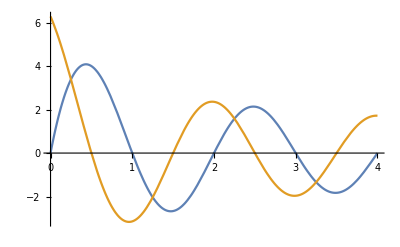

```mathematica
totalEnergy/.{kd->0,ks->1}
Plot[{Im[%],Re[%]},{shininess,0,4}]
```

Sin[1/2 (ϕ_i-ϕ_v)]^8

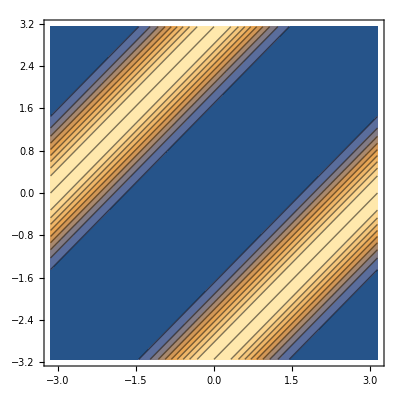

```mathematica
lockTheta/.{shininess->4,kd->0,ks->1}//FullSimplify

ContourPlot[%,{Subscript[ϕ, v],-Pi,Pi},{Subscript[ϕ, i],-Pi,Pi}]
```

```mathematica
Syma
```

```mathematica
sarray=SymmetrizedArray[array]
```

```mathematica
cov=RandomReal[{0,1},{3,3}];
cov = Transpose[cov].cov;
dist=MultinormalDistribution[{0,0,0},cov]
PDF[dist,{x,y,z}]
```

MultinormalDistribution[{0,0,0},{{0.627698,0.870387,0.656244},{0.870387,1.39844,1.19295},{0.656244,1.19295,1.21765}}]

0.543609 ⅇ^(1/2 (-y (-20.3018 x+24.458 y-13.0203 z)-z (8.84095 x-13.0203 y+8.81267 z)-x (20.5012 x-20.3018 y+8.84095 z)))

```mathematica
n=5;
resolution=32;

points=RandomReal[{-1,1},{n,3}]
vals=Sign@Threshold[Range[n],n*3/4]
nearest=Nearest[points]
nearestColor=Nearest[points->Transpose[{points,RandomColor[n]}]];
Graphics3D[Ball/@points,ViewAngle->90*Degree,ViewVertical->{0, 1, 0},ViewPoint->{0, 0, 1}]


gen=Round@*Mean@*Nearest[points->vals];
ClearAll[gen];
signedDistSample[v_]:=(Norm[v-First@nearest[v],2]-0.5);

getSurfaceInfo[v_]:=Module[{color,center,normal},
{center,color}=First[nearestColor[v]];
normal=Normalize[v-center];
{color,normal}
];

gen=Boole@*Negative@*signedDistSample
(*ClearAll[gen];gen[v_]:=Boole[Min[Norm[v-0.5]-0.3,Norm[v-0.7,1]-0.2]<0];*)


img=Image3D[Array[gen@*List,resolution{1,1,1},{{0,1},{0,1},{0,1}}],"Bit"];
signedDistField=DistanceTransform[ColorNegate@img]-(DistanceTransform[img]-img);
signedDistField=ImageMultiply[signedDistField,1/resolution];
signedDistFieldGrad=GradientFilter[signedDistField,1];
worldToImageTransform[p_]:=(Clip[p]+1)/2*resolution
```

{{-0.205022,-0.876315,-0.633799},{0.41635,0.367569,-0.865607},{0.876451,-0.238237,0.9467},{-0.716713,-0.317847,-0.0622268},{0.468816,0.460456,0.953959}}

{0,0,0,1,1}

NearestFunction[{3, <>}]

-Graphics3D-

Boole@*Negative@*signedDistSample

```mathematica
ClearAll[rayTrace]
maxNumSteps=resolution;

rayTraceSimple[startPos_,dir_,maxsteps_]:=Module[{pos=startPos,dist=0,stepSize,val,hit=False,step=maxsteps},
Do[
val=ImageValue[img,pos,DataRange->Automatic];
(*Print[{Norm[pos-0.5],val}];*)
hit=val≥0.9;
If[hit,step=s;Break[]];

stepSize=ImageValue[signedDistField,pos,DataRange->Automatic];
stepSize=0.1;
dist+=stepSize;
pos=startPos+dir*dist;
,
{s,0,maxsteps}];
Return[{dist,step}];
];

rayTrace[startPos_,dir_,maxsteps_]:=Module[{pos=startPos,
dist=0,
stepScale=1.5,
color=Transparent,normal={0,0,0},
stepSize,val,hit=False,step=maxsteps},
Do[
If[dist>maxDist,dist=maxDist;step=s;Break[]];
val=signedDistSample[pos];
(*Print[{Norm[pos-0.5],val}];*)
hit=Abs[val]<0.01;
If[hit,
step=s;
{color,normal}=getSurfaceInfo[pos];
Break[]
];

stepSize=stepScale*val;
dist+=stepSize;
pos=startPos+dir*dist;
,
{s,0,maxsteps}];
Return[{color,normal,dist,step}];
];

maxDist=5;
startPos={0,0,-2};
ImageValue[img,startPos]==0
renderRes=64;
renderResStep=1/(renderRes-1);
render[t_,s_]:=rayTrace[startPos,N@Normalize@{2t-1,2s-1,1},maxNumSteps];
rendered=Parallelize@Table[render[t,s],{t,1,0,-renderResStep},{s,0,1,renderResStep}];

Image[rendered[[;;,;;,1]]];
RemoveAlphaChannel[%]
Image[rendered[[;;,;;,2]]*0.5+0.5]
Image[rendered[[;;,;;,4]]/maxNumSteps]
```

True

-Graphics-

-Graphics-

-Graphics-

```mathematica
{
{1,1,0},
{0,0,0}
}
```

{{1,1,0},{0,0,0}}

DSolve::deqx: Supplied equations are not differential equations of the given functions.

DSolve[{f[0]==0},f[x],x]

```mathematica
ClearAll[smoothStep]
smoothStep[x_]:=Clip[6x^5-15x^4+10x^3,{0,1}]
smoothStep[x_]:=Piecewise[{{0,x≤0},{1,x≥1}},6x^5-15x^4+10x^3]
smoothSquare[x_]:=smoothStep[2*TriangleWave[x]]
smoothSquare[x_,duty_]:=smoothStep[TriangleWave[-1+2(duty+{-1,1}),x]]
```

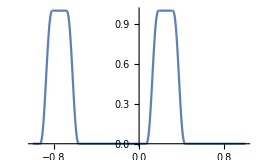

```mathematica
Plot[smoothSquare[a,1/4],{a,-1,1}]
```

```mathematica
{r,a}=ToPolarCoordinates[{x,y}]
implicit=r≤1-0.1smoothSquare[a*23/(2Pi),.3];
```

{√(x^2+y^2),ArcTan[x,y]}

```mathematica
Region@ImplicitRegion[implicit,{x,y}]
```

ImplicitRegion[√(x^2+y^2)≤1-0.1 (Piecewise[{{0, TriangleWave[{-2.4,1.6},(23 ArcTan[x,y])/(2 π)]≤0}, {1, TriangleWave[{-2.4,1.6},(23 ArcTan[x,y])/(2 π)]≥1}, {10 TriangleWave[{-2.4,1.6},(23 ArcTan[x,y])/(2 π)]^3-15 TriangleWave[{-2.4,1.6},(23 ArcTan[x,y])/(2 π)]^4+6 TriangleWave[{-2.4,1.6},(23 ArcTan[x,y])/(2 π)]^5, True}}]),{x,y}]